-Graphics3D-

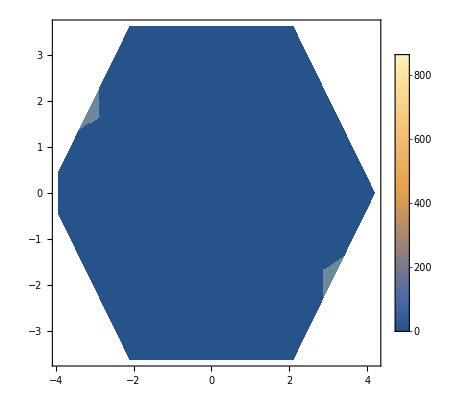

```mathematica
(*data import*)
dataLoc=StringJoin[NotebookDirectory[],"dataOut/strFct.dat"];
dataStrFct=Import[dataLoc];
(*basic settings*)
numCellX=24;
numCellY=24;
(*******************************************************************)
numCell=numCellX numCellY;
sphToCar[coorSph_]:={Sin[coorSph⟦1⟧]Cos[coorSph⟦2⟧],Sin[coorSph⟦1⟧]Sin[coorSph⟦2⟧],Cos[coorSph⟦1⟧]};
coorToCode[coor_]:=1+coor⟦1⟧+coor⟦2⟧numCellX+coor⟦3⟧numCell;
codeToCoor[code_]:=Module[{remain,coor1,coor2,coor3},
remain=code-1;
coor3=Floor[remain/numCell];
remain=remain-coor3 numCell;
coor2=Floor[remain/numCellX];
coor1=remain-coor2 numCellX;
{coor1,coor2,coor3}
];
err[data_]:=Module[{len,sumSq,meanData},
len=Length[data];
sumSq=Sum[data⟦i⟧^2,{i,1,len}];
meanData=Mean[data];
√((sumSq-len meanData^2)/(len(len-1)))
];
uniX={1,0}//N;
uniY={1/2,(√3)/2}//N;
uniC={0,1/(√3)}//N;
uniKX=(4 √3 π)/(3numCellX){(√3)/2,-1/2}//N;
uniKY=(4 √3 π)/(3numCellY){0,1}//N;
vecRListA=Table[Module[{coorTemp},
coorTemp=codeToCoor[i];
coorTemp⟦1⟧uniX+coorTemp⟦2⟧uniY
],{i,1,numCell}];
vecRListB=Table[Module[{coorTemp},
coorTemp=codeToCoor[i+numCell];
coorTemp⟦1⟧uniX+coorTemp⟦2⟧uniY+uniC
],{i,1,numCell}];
vecRList=Join[vecRListA,vecRListB];
vecKList=Table[Module[{coorTemp},
coorTemp=codeToCoor[i];
coorTemp⟦1⟧uniKX+coorTemp⟦2⟧uniKY
],{i,1,numCell}];
uniKX=(4 √3 π)/(3numCellX){(√3)/2,-1/2}//N;
uniKY=(4 √3 π)/(3numCellY){0,1}//N;
vecKList=Table[Module[{coorTemp},
coorTemp=codeToCoor[i];
coorTemp⟦1⟧uniKX+coorTemp⟦2⟧uniKY
],{i,1,numCell}];
(*define the first Brillouin zone*)
cornorList={
2π{1/3,(√3)/3},
-2π{1/3,(√3)/3},
2π{-1/3,(√3)/3},
-2π{-1/3,(√3)/3},
2π{2/3,0},
-2π{2/3,0}
}//N;
borderList={
{cornorList⟦1⟧,cornorList⟦5⟧},
{cornorList⟦5⟧,cornorList⟦4⟧},
{cornorList⟦4⟧,cornorList⟦2⟧},
{cornorList⟦2⟧,cornorList⟦6⟧},
{cornorList⟦6⟧,cornorList⟦3⟧},
{cornorList⟦3⟧,cornorList⟦1⟧}
};
graBZ=Graphics[{Red,Line[borderList]}];
strFacGen[dataStr_]:=Module[{data1,data2,data3,data4},
data1=Table[Append[vecKList⟦i⟧,dataStr⟦i,3⟧],{i,1,numCell}];
data2=Table[Append[vecKList⟦i⟧-uniKX numCellX,dataStr⟦i,3⟧],{i,1,numCell}];
data3=Table[Append[vecKList⟦i⟧-uniKY numCellY,dataStr⟦i,3⟧],{i,1,numCell}];
data4=Table[Append[vecKList⟦i⟧-uniKX numCellX-uniKY numCellY,dataStr⟦i,3⟧],{i,1,numCell}];
Join[data1,data2,data3,data4]
];
strFac=strFacGen[dataStrFct];
pointIn={};
Table[Module[{data,judA,judB,jud},
data=strFac⟦pointInd⟧;
judA=Product[If[data⟦2⟧≤(borderList⟦i,2,2⟧-borderList⟦i,1,2⟧)/(borderList⟦i,2,1⟧-borderList⟦i,1,1⟧)(data⟦1⟧-borderList⟦i,1,1⟧)+borderList⟦i,1,2⟧,1,0],{i,{1,5,6}}];
judB=Product[If[data⟦2⟧≥(borderList⟦i,2,2⟧-borderList⟦i,1,2⟧)/(borderList⟦i,2,1⟧-borderList⟦i,1,1⟧)(data⟦1⟧-borderList⟦i,1,1⟧)+borderList⟦i,1,2⟧,1,0],{i,{2,3,4}}];
jud=judA judB;
If[jud==1,pointIn=Append[pointIn,pointInd]];
],{pointInd,1,Length[strFac]}];
strFacIn=Table[strFac⟦i⟧,{i,pointIn}];
gra3D=ListPlot3D[strFacIn,PlotRange->All,Mesh->None,ColorFunction->"TemperatureMap",Boxed->False,Axes->{True,True,False},AxesLabel->{"k_x","k_y"}];
graDen=ListDensityPlot[strFacIn,PlotRange->All,PlotLegends->Automatic];
Export[StringJoin[NotebookDirectory[],"strFct3D.eps"],gra3D];
Export[StringJoin[NotebookDirectory[],"strFctDen.eps"],graDen];
Export[StringJoin[NotebookDirectory[],"strFct3D.png"],gra3D];
Export[StringJoin[NotebookDirectory[],"strFctDen.png"],graDen];
Show[gra3D]
Show[graDen]
```

```mathematica
dataStrFct//MatrixForm
```

(0 | 0 | 0.000136572
0.523599 | -0.3023 | 0.000022173
1.0472 | -0.6046 | 0.000134013
1.5708 | -0.9069 | 0.0000517219
2.0944 | -1.2092 | 0.0000267878
2.61799 | -1.5115 | 0.0000960833
3.14159 | -1.8138 | 0.000107167
3.66519 | -2.1161 | 0.000144935
4.18879 | -2.4184 | 0.000258847
4.71239 | -2.7207 | 0.000122155
5.23599 | -3.023 | 0.00012668
5.75959 | -3.3253 | 0.0000873602
0 | 0.6046 | 0.0000320433
0.523599 | 0.3023 | 0.0000450059
1.0472 | 0 | 0.000266743
1.5708 | -0.3023 | 0.000230065
2.0944 | -0.6046 | 0.0000789179
2.61799 | -0.9069 | 0.000127402
3.14159 | -1.2092 | 0.000200884
3.66519 | -1.5115 | 0.0000697923
4.18879 | -1.8138 | 0.0000227217
4.71239 | -2.1161 | 0.000264949
5.23599 | -2.4184 | 0.0000545378
5.75959 | -2.7207 | 0.000168069
0 | 1.2092 | 0.0000989789
0.523599 | 0.9069 | 0.0000764364
1.0472 | 0.6046 | 0.0000446029
1.5708 | 0.3023 | 0.000114164
2.0944 | 0 | 0.0000861123
2.61799 | -0.3023 | 0.000199878
3.14159 | -0.6046 | 0.000236043
3.66519 | -0.9069 | 0.0000341451
4.18879 | -1.2092 | 0.0000242388
4.71239 | -1.5115 | 0.0000589563
5.23599 | -1.8138 | 0.000549136
5.75959 | -2.1161 | 0.000337323
0 | 1.8138 | 0.00020047
0.523599 | 1.5115 | 0.0000231205
1.0472 | 1.2092 | 0.000155144
1.5708 | 0.9069 | 0.000122418
2.0944 | 0.6046 | 0.000045519
2.61799 | 0.3023 | 0.000129274
3.14159 | 0 | 0.000166159
3.66519 | -0.3023 | 0.000300936
4.18879 | -0.6046 | 0.000220999
4.71239 | -0.9069 | 0.0000313071
5.23599 | -1.2092 | 0.000151344
5.75959 | -1.5115 | 0.0001717
0 | 2.4184 | 0.0001261
0.523599 | 2.1161 | 0.0000950182
1.0472 | 1.8138 | 0.000121605
1.5708 | 1.5115 | 0.0000838378
2.0944 | 1.2092 | 0.000105753
2.61799 | 0.9069 | 0.000292896
3.14159 | 0.6046 | 0.000104432
3.66519 | 0.3023 | 0.000549317
4.18879 | 0 | 0.000165252
4.71239 | -0.3023 | 0.000443286
5.23599 | -0.6046 | 0.0000108834
5.75959 | -0.9069 | 0.000133994
0 | 3.023 | 0.000105707
0.523599 | 2.7207 | 0.000151793
1.0472 | 2.4184 | 0.000149962
1.5708 | 2.1161 | 0.000130334
2.0944 | 1.8138 | 0.0000155456
2.61799 | 1.5115 | 0.000156485
3.14159 | 1.2092 | 0.000110898
3.66519 | 0.9069 | 0.000290233
4.18879 | 0.6046 | 0.00005136
4.71239 | 0.3023 | 0.0000585336
5.23599 | 0 | 0.0000332117
5.75959 | -0.3023 | 0.000213326
0 | 3.6276 | 0.000182763
0.523599 | 3.3253 | 0.0000623016
1.0472 | 3.023 | 0.0000385011
1.5708 | 2.7207 | 0.0000944887
2.0944 | 2.4184 | 0.000208976
2.61799 | 2.1161 | 0.000207679
3.14159 | 1.8138 | 0.0000974904
3.66519 | 1.5115 | 0.000105865
4.18879 | 1.2092 | 0.000120333
4.71239 | 0.9069 | 0.0000799127
5.23599 | 0.6046 | 0.00015147
5.75959 | 0.3023 | 0.00018544
0 | 4.2322 | 0.000144842
0.523599 | 3.9299 | 0.0002453
1.0472 | 3.6276 | 0.000179946
1.5708 | 3.3253 | 0.0000867863
2.0944 | 3.023 | 0.0000940503
2.61799 | 2.7207 | 0.000232467
3.14159 | 2.4184 | 0.00006693
3.66519 | 2.1161 | 0.0000386672
4.18879 | 1.8138 | 0.000132462
4.71239 | 1.5115 | 0.000120233
5.23599 | 1.2092 | 0.0000992792
5.75959 | 0.9069 | 0.000345974
0 | 4.8368 | 0.00020319
0.523599 | 4.5345 | 0.000223849
1.0472 | 4.2322 | 0.0000173576
1.5708 | 3.9299 | 0.000112967
2.0944 | 3.6276 | 0.0000636017
2.61799 | 3.3253 | 0.00051436
3.14159 | 3.023 | 0.000336302
3.66519 | 2.7207 | 0.000270061
4.18879 | 2.4184 | 0.000335893
4.71239 | 2.1161 | 0.000206671
5.23599 | 1.8138 | 0.0000497648
5.75959 | 1.5115 | 0.000185487
0 | 5.4414 | 0.00020014
0.523599 | 5.1391 | 0.000410476
1.0472 | 4.8368 | 0.000138207
1.5708 | 4.5345 | 0.000114785
2.0944 | 4.2322 | 0.000376047
2.61799 | 3.9299 | 0.000264973
3.14159 | 3.6276 | 0.000250801
3.66519 | 3.3253 | 0.000354111
4.18879 | 3.023 | 0.000107128
4.71239 | 2.7207 | 0.000019623
5.23599 | 2.4184 | 0.000218878
5.75959 | 2.1161 | 0.0000432233
0 | 6.046 | 0.000106879
0.523599 | 5.7437 | 0.000113875
1.0472 | 5.4414 | 0.00112035
1.5708 | 5.1391 | 0.000261053
2.0944 | 4.8368 | 0.0000651093
2.61799 | 4.5345 | 0.000110986
3.14159 | 4.2322 | 0.000159266
3.66519 | 3.9299 | 0.000244313
4.18879 | 3.6276 | 0.0000260172
4.71239 | 3.3253 | 0.000109073
5.23599 | 3.023 | 0.000149522
5.75959 | 2.7207 | 0.000154413
0 | 6.6506 | 0.000166736
0.523599 | 6.3483 | 0.000209879
1.0472 | 6.046 | 0.0000742636
1.5708 | 5.7437 | 0.000139024
2.0944 | 5.4414 | 0.0000680085
2.61799 | 5.1391 | 0.00016696
3.14159 | 4.8368 | 0.000218862
3.66519 | 4.5345 | 0.0000281462
4.18879 | 4.2322 | 0.000156353
4.71239 | 3.9299 | 0.000198462
5.23599 | 3.6276 | 0.000213517
5.75959 | 3.3253 | 0.0000708847)